Drug Equations
A - Cocaine and related drugs

Sample 1

```mathematica
endtime = 10;
A = 3;
k = 2.5;
starter = 0.00125;
Clear[t,y,Derivative];
solution = 
 NDSolve[{y'[t] == -(k y[t])/(A+y[t]), 
            y[0] == starter},y[t],{t,0,endtime}];
coke[t_] = y[t]/.solution[[1]];

cokeplot = Plot[{coke[t]},{t,0,endtime},
       AxesLabel->{"t","cocaine"},PlotRange->All, PlotStyle->{Thickness[.025],Hue[.2]}];
```

```mathematica
endtime = 10;
A = 3;
k = 2.5;
starter = 0.00125;
Clear[t,y,Derivative];
solution = 
 NDSolve[{y'[t] == -(k y[t])/A, 
            y[0] == starter},y[t],{t,0,endtime}];
coke[t_] = y[t]/.solution[[1]];

simplifiedcokeplot = Plot[{coke[t]},{t,0,endtime},
       AxesLabel->{"t","cocaine"},PlotRange->All];
```

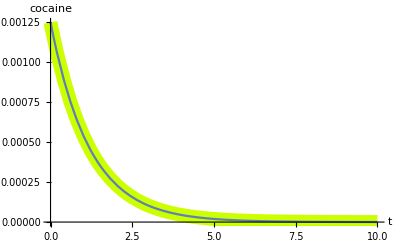

```mathematica
Show[cokeplot, simplifiedcokeplot]
```

```mathematica
endtime = 10;
Clear[A, k, starter]
A = 5;
k = 2;
starter = 0.00345;
Clear[t,y,Derivative];
solution = 
 NDSolve[{y'[t] == -(k y[t])/(A+y[t]), 
            y[0] == starter},y[t],{t,0,endtime}];
coke[t_] = y[t]/.solution[[1]];

cokeplot = Plot[{coke[t]},{t,0,endtime},
       AxesLabel->{"t","cocaine"},PlotRange->All, PlotStyle->{Thickness[.025],Hue[.2]}];
```

```mathematica
endtime = 10;
Clear[A, k, starter]
A = 5;
k = 2;
starter = 0.00345;
Clear[t,y,Derivative];
solution = 
 NDSolve[{y'[t] == -(k y[t])/A, 
            y[0] == starter},y[t],{t,0,endtime}];
coke[t_] = y[t]/.solution[[1]];

simplifiedcokeplot = Plot[{coke[t]},{t,0,endtime},
       AxesLabel->{"t","cocaine"},PlotRange->All];
```

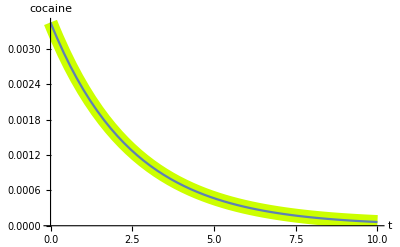

```mathematica
Show[cokeplot, simplifiedcokeplot]
```

The pharmacokineticists are justified in their replacement of the basic model for the simplified model because they are essentially the same / produce the same graph for small values of y(0) relative to A. 
Folks say that cocaine concentration decays exponentially because the graphs of the models reflect exponential decay, and because y is defined as a exponential function ( y(0) * e^(-kt/A)).

B Alcohol and related drugs

```mathematica
endtime = 10;
A = 0.001;
k = 0.02;
starter = 0.0037;
solution = 
 NDSolve[{y'[t] == -(k y[t])/(A+y[t]), 
            y[0] == starter},y[t],{t,0,endtime}];
alcohol[t_] = y[t]/.solution[[1]];

sloshplot = Plot[{alcohol[t]},{t,0,.4},
       AxesLabel->{"t","alcohol"},
       PlotRange->All];
```

```mathematica
endtime = 10;
A = 0.001;
k = 0.02;
starter = 0.0037;
solution = 
 NDSolve[{y'[t] == -k, 
            y[0] == starter},y[t],{t,0,endtime}];
alcohol[t_] = y[t]/.solution[[1]];

linearplot= Plot[{alcohol[t]},{t,0,.4},
       AxesLabel->{"t","alcohol"},
       PlotRange->All, PlotStyle->{Thickness[.025],Hue[.2]}];
```

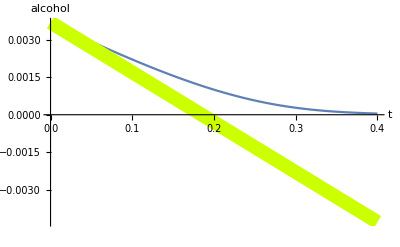

```mathematica
Show[sloshplot, linearplot]
```

```mathematica
iii
```

Most folks say that alcohol concentration decays linearly up until a point because the graph of the decay (graph 1) behaves in a practically linear way until x ≈ .2 . Furthermore, the graph of a linear function (graph 2) is positive until x ≈ .2. You can see that at some small alcohol level (“at which no one cares”), the graphs diverge

#### Epidemics

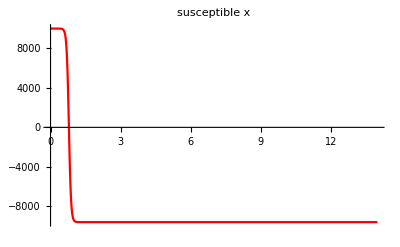

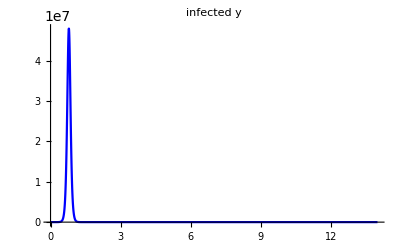

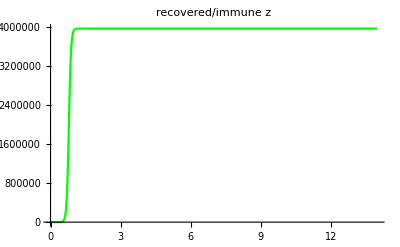

```mathematica
a=.00218;
b=.44036;
start=0;
stop=14;
susstart = 10000;
infstart = 10;
recovstart = 20;
sol=NDSolve[{{Sus'[t]==-a*Inf[t],Inf'[t]==a*Sus[t]*Inf[t]-b Inf[t], Recov'[t]==b*Inf[t]},{Sus[start]==susstart,Inf[start]==infstart, Recov[start]==recovstart}},{Sus[t],Inf[t], Recov[t]},{t,start,stop}];
Sus2[t_]=Sus[t]/.sol[[1,1]];
Inf2[t_]=Inf[t]/.sol[[1,2]];
Recov2[t_]=Recov[t]/.sol[[1, 3]];
plotsus=Plot[Sus2[t],{t,start,stop},PlotLabel->Row[{"susceptible ",Style["x",Italic]}],PlotStyle->Red,PlotRange->All]
plotinf=Plot[Inf2[t],{t,start,stop},PlotLabel->Row[{"infected ",Style["y",Italic]}],PlotStyle->Blue,PlotRange->All]
plotrecov = Plot[Recov2[t], {t, start, stop},
PlotLabel->Row[{"recovered/immune ", Style["z", Italic]}],
PlotStyle->Green, PlotRange->All]
```

The following analysis assumes that you select your starting conditions to reflect that of the beginning of a “real outbreak”, namely with a relatively large susceptible population and relatively small infected and recovered populations. After some (short) time period,  everyone who is susceptible gradually becomes infected (see the spike in the infected graph and the sudden drop in susceptibles). After someone leaves the category of “susceptible”, they must become infected, and then they can die or becomes “recovered”. This explains why Sus[t] only decreases and Recov[t] only increases. The spike in the infected graph characterizes the severity of the epidemic (front side) and the recovery of infected individuals (back side). I believe that the severity of the epidemic could reflect that of the well know outbreaks such as the bubonic plague.

```mathematica
ii
```

It makes sense that Sus’[t] <  0 because people can leave the “susceptible” category, but they cannot enter it once they are gone. Furthermore, people are constantly getting infected, so the number of susceptible people is constantly decreases. Hence, the rate of change is always negative.

```mathematica
iii
```

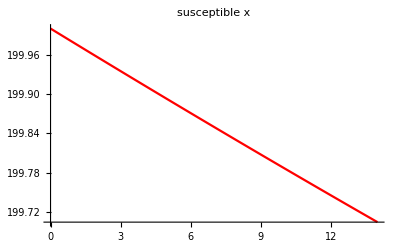

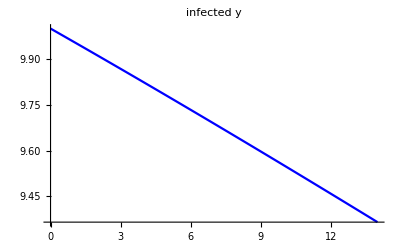

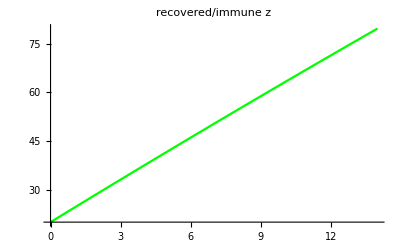

```mathematica
a=.00218;
b=.44036;
start=0;
stop=14;
susstart = 200;
infstart = 10;
recovstart = 20;
sol=NDSolve[{{Sus'[t]==-a*Inf[t],Inf'[t]==a*Sus[t]*Inf[t]-b Inf[t], Recov'[t]==b*Inf[t]},{Sus[start]==susstart,Inf[start]==infstart, Recov[start]==recovstart}},{Sus[t],Inf[t], Recov[t]},{t,start,stop}];
Sus2[t_]=Sus[t]/.sol[[1,1]];
Inf2[t_]=Inf[t]/.sol[[1,2]];
Recov2[t_]=Recov[t]/.sol[[1, 3]];
plotsus=Plot[Sus2[t],{t,start,stop},PlotLabel->Row[{"susceptible ",Style["x",Italic]}],PlotStyle->Red,PlotRange->All]
plotinf=Plot[Inf2[t],{t,start,stop},PlotLabel->Row[{"infected ",Style["y",Italic]}],PlotStyle->Blue,PlotRange->All]
plotrecov = Plot[Recov2[t], {t, start, stop},
PlotLabel->Row[{"recovered/immune ", Style["z", Italic]}],
PlotStyle->Green, PlotRange->All]
```

The previous graphs show the effect of a relatively small intial value for Sus(0) (where Sus(0) is less than b/a). Because there are so few susceptible people relative to what is usually seen in epidemics, the rate at which infected people recover is actually significant in reducing the number of infected people relative to the number of people to become infected. Thus, as usual, Sus(t) decreases with time, but Inf(t) also does and Recov’(t) > 0 for all t seen.
When Sus(0) is greater than b/a, the rate at which people become infected is more significant than the rate at which infected people recover, hence Inf’(t) > 0 for all t until Sus(t) becomes sufficiently small in which case the logic in the previous paragraph applies.

```mathematica
iv
```

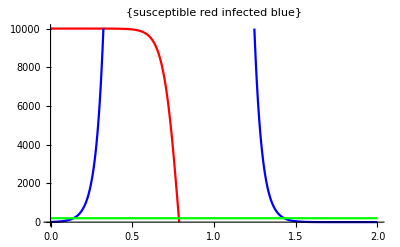

```mathematica
a=.00218;
b=.44036;
start=0;
stop=14;
susstart = 10000;
infstart = 10;
recovstart = 20;
sol=NDSolve[{{Sus'[t]==-a*Inf[t],Inf'[t]==a*Sus[t]*Inf[t]-b Inf[t], Recov'[t]==b*Inf[t]},{Sus[start]==susstart,Inf[start]==infstart, Recov[start]==recovstart}},{Sus[t],Inf[t], Recov[t]},{t,start,stop}];
Sus2[t_]=Sus[t]/.sol[[1,1]];
Inf2[t_]=Inf[t]/.sol[[1,2]];
Recov2[t_]=Recov[t]/.sol[[1, 3]];
plotall=Plot[{Sus2[t], Inf2[t], b/a},{t,0,2},PlotLabel->{"susceptible red infected blue"}, PlotStyle-> {Red, Blue, Green},PlotRange->{0, 10000}]
```

Sus[0] is clearly greater than b/a (shown by the red function above the green function at t = 0. This corroborates part 3 and part 2 because an epidemic occurs and hence the number of susceptible people continually decreases. Graphically, the plot range was set up to 10000, meaning that if the function ever increased, it would go out of the window (given Sus[0] = 10000).